# Matematična umetnost: Generiranje slik s formulami

Ta projekt raziskuje generativno umetnost s pomočjo matematičnih enačb in fraktalnih algoritmov v Wolfram Mathematica. Cilj je ustvariti vizualno privlačne slike in interaktivne vzorce z uporabo funkcij, kot so Mandelbrotova in Julia množica, Barnsleyjev praproti fraktal ter parametrično generirane krivulje.

## Formule:

Mandelbrotova množica:   z_(n+1)=z_n^2+c
Julia množica: z_(n+1)=z_n^2+c (s stalnim c)
Barnsleyjev praproti fraktal: Afinske transformacije z različnimi verjetnostmi
Parametrične krivulje: x(t) = f_1(t), y(t) = f_2(t)

## 1. Mandelbrotova množica

Implementacija Mandelbrotove množice z barvno shemo. Za hitrejše izvajanje je uporabljena funkcija Compile.

```mathematica
mandelbrotPlot=Rasterize[DensityPlot[mandelbrotCompiled[x,y,100],{x,-2,1},{y,-1.5,1.5},PlotPoints->400,ColorFunction->"SunsetColors",Mesh->False,Frame->False]];
```

```mathematica
mandelbrotPlot
```

-Graphics-

## 2. Julia množica

Julia množice so zelo podobne Mandelbrotovi množici, le da uporabljajo fiksno kompleksno število c, medtem ko se z spreminja. Spodaj uporabimo interaktivno vizualizacijo z uporabo Manipulate.

```mathematica
juliaFn[x_,y_,re_,im_,max_]:=Module[{z=x+I y,c=re+I im,n=0},While[Abs[z]<=2&&n<max,z=z^2+c;n++];n]
Manipulate[DensityPlot[juliaFn[x,y,re,im,100],{x,-1.5,1.5},{y,-1.5,1.5},PlotPoints->300,ColorFunction->"Rainbow",Frame->False],{{re,-0.7},-1,1},{{im,0.27015},-1,1}]
```

## 3. Barnsleyjev praproti fraktal

Barnsleyjev praproti fraktal je generiran z afinskimi transformacijami z določenimi verjetnostmi. To ustvari realistično simulacijo listov praproti.

```mathematica
Manipulate[Module[{x=0.,y=0.,points={},r},Do[r=RandomReal[];{x,y}=Which[r<0.01,{0,0.16 y},r<0.86,{0.85 x+0.04 y,-0.04 x+0.85 y+1.6},r<0.93,{0.2 x-0.26 y,0.23 x+0.22 y+1.6},True,{0.28 y-0.15 x,0.26 x+0.24 y+0.44}];AppendTo[points,{x,y}],{n}];Graphics[{Directive[color,PointSize[size]],Point[points]},PlotRange->{{-3,3},{0,10}},Background->White]],{{n,10000},1000,100000,1000},{{size,0.001},0.0001,0.005,Appearance->"Labeled"},{{color,Green},{Green,Blue,Red,Purple,Darker[Green]}}]
```

## 4. Parametrične krivulje

Z uporabo sinusnih in kosinusnih funkcij ustvarimo estetske parametrične krivulje, ki so pogosto videti kot cvetovi ali geometrijski vzorci.

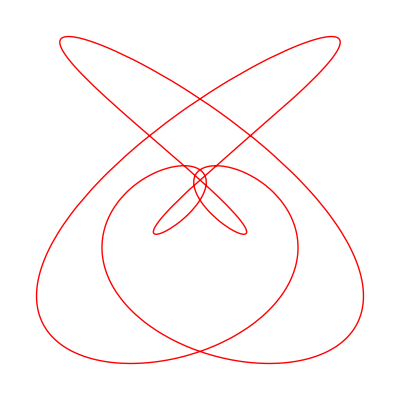

```mathematica
curvePlot=ParametricPlot[{Sin[3 t]+Cos[5 t],Sin[4 t]-Cos[2 t]},{t,0,2 π},PlotStyle->{Thick,Red},Axes->False,AspectRatio->1]
```

## 5. Interaktivna vizualizacija parametričnih krivulj

Z uporabo funkcije Manipulate lahko spreminjamo parametre parametričnih funkcij in s tem interaktivno raziskujemo različne oblike.

```mathematica
Manipulate[ParametricPlot[{Sin[a t]+Cos[b t],Sin[c t]-Cos[d t]},{t,0,2 π},PlotStyle->{Thick,Blue},Axes->False,AspectRatio->1],{{a,3},1,10,1},{{b,5},1,10,1},{{c,4},1,10,1},{{d,2},1,10,1}]
```

## 6. Animacija Mandelbrotove množice

S pomočjo ListAnimate lahko ustvarimo animacijo, kjer se število iteracij povečuje . Tako dobimo občutek, kako kompleksnost fraktala raste .

```mathematica
frames=Table[DensityPlot[mandelbrotCompiled[x,y,50+i],{x,-2,1},{y,-1.5,1.5},PlotPoints->200,ColorFunction->"DeepSeaColors",Frame->False],{i,0,50,5}];
```

```mathematica
ListAnimate[frames]
```